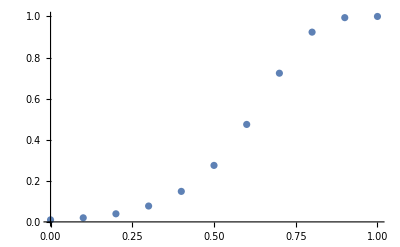
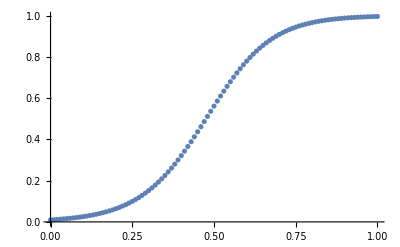
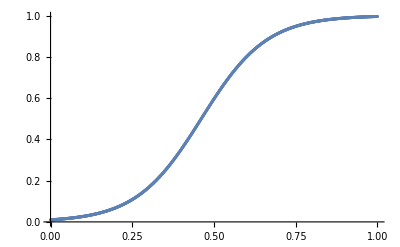

```mathematica
EulerExplicit[f_,t0_,x0_,T_,h_]:=Module[
{n=⌈(T-t0)/h⌉,t,x,k},
t=Table[t0+k*h,{k,0,n}];
x=ConstantArray[0,n+1];
x⟦1⟧=x0;

For[k=1,k≤n,k++,
x⟦k+1⟧=x⟦k⟧+h*f[t⟦k⟧,x⟦k⟧];
];

{t,x}
]

(* Example *)
f[t_,u_]:=10*u*(1-u);
x0=N@0.01;
t0=0;
T=N@1;
hArr=Table[10^-i,{i,1,3}];
(sol=EulerExplicit[f,t0,x0,T,#];
n=Length@sol⟦1⟧;
ListPlot[Table[{sol⟦1,k⟧,sol⟦2,k⟧},{k,1,n}]])&/@hArr
```